## GEP 2/26

Model of the NaCs tweezer array during a Ramsey pulse with dipolar interactions between the molecules. Each of the eight sites in the array has a probability of being filled, called the ‘filling fraction.’ The sites are spaced out according to a metric called the ‘arrayGeometry’, which determines the spacing between each site. I initialize the array in the ground state, apply a global pi/2 pulse, and allow free procession for a time t in the presence of dipolar interactions. I then apply a reverse global pi/2 pulse. The code shows that as the filling fraction increases the population that returns to the ground state approaches half contrast.

### Setup

```mathematica
kp[x_]:=If[Length[x]==1∨SameQ[x,IdentityMatrix[2]],x,KroneckerProduct@@x]

nℋ1=2;
ℋ1=IdentityMatrix[nℋ1];
sℋ1=Partition[ℋ1,{nℋ1,1}][[1]];
lℋ1=Range[0,nℋ1-1];
s2lℋ1=AssociationThread[sℋ1->lℋ1] ;
l2sℋ1=AssociationThread[lℋ1->sℋ1]; 

σx=PauliMatrix[1];σy=PauliMatrix[2];σz=PauliMatrix[3];σp=(σx+ⅈ σy)/2;σm=(σx-ⅈ σy)/2;id=IdentityMatrix[2];

arrayGeometry={1,0,1,0,0,1,0,1,0,0,1,0,1,0,0,1,0,1};
arrayPos=Flatten[Position[arrayGeometry,1]];(*Position of the sites in the array geometry*)
siteNumber=Length[arrayPos];
fillingFraction=0.4;
```

### Array geometry

```mathematica
ψList={};Do[siteFilling=RandomVariate[BernoulliDistribution[fillingFraction],siteNumber];i=0;While[Total[siteFilling]==0,siteFilling=RandomVariate[BernoulliDistribution[fillingFraction],siteNumber];i++];
(*While[siteFilling[[{1,2}]]!={1,1},siteFilling=RandomVariate[BernoulliDistribution[fillingFraction],siteNumber];i++];*)
sitePos=Flatten[Position[siteFilling,1]];
fillingNumber=Length[sitePos];
siteDistances=Select[Flatten[Table[{i,j,5(arrayPos[[sitePos[[j]]]]-arrayPos[[sitePos[[i]]]])},{i,Range[fillingNumber]},{j,Range[fillingNumber]}],1],#[[3]]>0&];
nP=fillingNumber;
nℋn=nℋ1^nP;
lℋn=Tuples[lℋ1,nP];
ℋn=IdentityMatrix[nℋn];
sℋn=Partition[ℋn,{nℋn,1}][[1]];
s2lℋn=AssociationThread[sℋn->lℋn];
l2sℋn=AssociationThread[lℋn->sℋn];
idArray=If[nP==1,id,ConstantArray[id,nP]];
σxℋn=If[nP==1,σx/2,Sum[kp[ReplacePart[idArray,p->σx/2]],{p,1,nP}]];numℋn[p_]:=If[nP==1,σp.σm,kp[ReplacePart[idArray,p->σp.σm]]];
numAvgℋn=Sum[numℋn[p]/nP,{p,1,nP}];
ddℋn[{site1_,site2_,distance_}]:=1/distance^3(kp[ReplacePart[idArray,{site1->σp,site2->σm}]]+kp[ReplacePart[idArray,{site1->σm,site2->σp}]]);
idℋn=kp[idArray];
ψ0=If[nP==1,l2sℋ1[0],kp[ConstantArray[l2sℋ1[0],nP]]];
op1=N[σxℋn];
op2=N[idℋn+Total[ddℋn[#]&/@siteDistances]];
tRange=Range[0,100000,500];
ψtab=ParallelTable[MatrixExp[ⅈ op1 π/2].MatrixExp[-ⅈ op2 t].MatrixExp[-ⅈ op1 π/2].ψ0,{t,tRange}];
ntab=ParallelTable[N[ψtab[[j]]†.numAvgℋn.ψtab[[j]]][[1,1]],{j,1,Length[tRange]}];
AppendTo[ψList,ntab],100
]
```

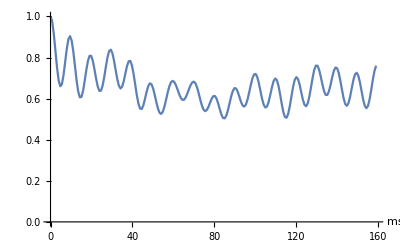

{0,0,0,0,0,1,1,1}

```mathematica
ListPlot[Transpose@{tRange/π 5 10^-3,Mean[ψList]},PlotRange->{0,1},Joined->True,AxesLabel->{"ms",""}]
siteFilling
```

```mathematica
siteFilling=RandomVariate[BernoulliDistribution[0.2],siteNumber];i=0;While[Total[siteFilling]==0,siteFilling=RandomVariate[BernoulliDistribution[0.2],siteNumber];i++]
sitePos=Flatten[Position[siteFilling,1]];
fillingNumber=Length[sitePos];
siteDistances=Select[Flatten[Table[{i,j,5(arrayPos[[sitePos[[j]]]]-arrayPos[[sitePos[[i]]]])},{i,Range[fillingNumber]},{j,Range[fillingNumber]}],1],#[[3]]>0&]
```

{{1,2,50},{1,3,60},{2,3,10}}

### States

#### Single particle

#### Multi-particle

```mathematica
nP=fillingNumber;
nℋn=nℋ1^nP;
lℋn=Tuples[lℋ1,nP];
ℋn=IdentityMatrix[nℋn];
sℋn=Partition[ℋn,{nℋn,1}][[1]];
s2lℋn=AssociationThread[sℋn->lℋn];
l2sℋn=AssociationThread[lℋn->sℋn];
```

### Operators

```mathematica
idArray=If[nP==1,id,ConstantArray[id,nP]];
σxℋn=If[nP==1,σx/2,Sum[kp[ReplacePart[idArray,p->σx/2]],{p,1,nP}]];numℋn[p_]:=If[nP==1,σp.σm,kp[ReplacePart[idArray,p->σp.σm]]];
numAvgℋn=Sum[numℋn[p]/nP,{p,1,nP}];
ddℋn[{site1_,site2_,distance_}]:=1/distance^3(kp[ReplacePart[idArray,{site1->σp,site2->σm}]]+kp[ReplacePart[idArray,{site1->σm,site2->σp}]])
idℋn=kp[idArray];
```

### Evolution

```mathematica
ψ0=If[nP==1,l2sℋ1[0],kp[ConstantArray[l2sℋ1[0],nP]]];
op1=N[σxℋn];
op2=N[idℋn+Total[ddℋn[#]&/@siteDistances]];
tRange=Range[0,5000,10];
```

```mathematica
ψtab=Table[MatrixExp[ⅈ op1 π/2].MatrixExp[-ⅈ op2 t].MatrixExp[-ⅈ op1 π/2].ψ0,{t,tRange}];
```

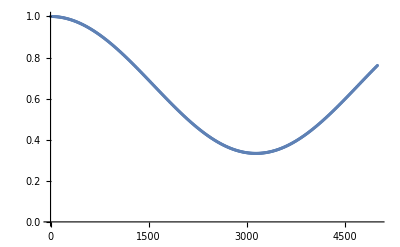

```mathematica
ListPlot[Table[{tRange[[j]],N[ψtab[[j]]†.numAvgℋn.ψtab[[j]]][[1,1]]},{j,1,Length[tRange]}],PlotRange->{0,1}]
```

The dipolar interaction at a distance of 1 has a pi time of π. The microwave pi time is also π. In the experiment the microwave pi time is order 5 us, whereas the dipolar interaction pi time is order 5 ms. The distance between two dipoles should therefore be 1000^(1/3)=10 so that the relative rates correspond.

Dot::dotsh: Tensors {{0,1,0,0}} and … have incompatible shapes.

Dot::dotsh: Tensors … and {{0},{1},{0},{0}} have incompatible shapes.

Dot::dotsh: Tensors {{0.,1.,0.,0.}} and … have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

-Graphics-

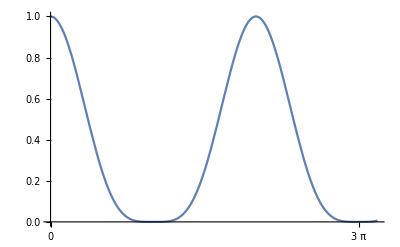

```mathematica
Plot[Abs[kp[{l2sℋ1[0],l2sℋ1[1]}]†.MatrixExp[-ⅈ ddℋn[{1,2,1}]t].kp[{l2sℋ1[0],l2sℋ1[1]}]]^2,{t,0,10},Ticks->{Range[0,10π,π],Automatic}]
Plot[Abs[kp[{l2sℋ1[0],l2sℋ1[0]}]†.MatrixExp[-ⅈ (kp[{id,σx/2}]+kp[{σx/2,id}])t].kp[{l2sℋ1[0],l2sℋ1[0]}]]^2,{t,0,10},Ticks->{Range[0,10π,π],Automatic}]
```

π is 5 us. t=100000 in the simulation is 160 ms.

```mathematica
20000/π*5 10^-3//N
```

31.831

31.831